# Study When Different Turing Machines Compute the Same Function

In this essay, we say that setting a Turing machine to a nonnegative integer  refers to filling the cells of the tape between  and  for some specified  with the binary representation of  with the least significant bit at position . We ensure that  (the number of bits fits in ). Additionally, we say the value of a Turing machine is the number created by the binary digits from cells  to .

## Formalism

Let  be the set of all -state -color Turing machines. Each Turing machine in  represents a partial function  with input specified by the base  number formed by an interval  on the tape, where each color is an integer between 0 and . Define two Turing machines in  to be isomorphic if they compute the same partial function on , or both do not exist. 
1. Determine the cardinality of  if two isomorphic Turing machines are considered equivalent.
2. For each distinct function (class of isomorphic Turing machines), determine and analyze the range of worst-case running times.

## Existing Work

We will begin by recreating the results shown on page 761 of Stephen Wolfram’s A New Kind of Science. Wolfram found that the space of all 2-state 2-color Turing machines represents exactly 351 distinct functions.

We will first create a function that simulates the evolution of a Turing machine with a tape set to some  with rule  until it reaches a halt state. Wolfram’s halt state was for the head to move to the right of its starting position (where the digits are not defined). Clearly, not all Turing machines will halt, so we will need to set a maximum iteration count. Also, for now, only four bit numbers will be used, which can represent numbers from 0 to 15.

Initialize rules and max iteration count:

```mathematica
states=2;
colors=2;
maxiters=128;
rules=Range[0,(2*states*colors)^(states*colors)-1];
bits=4;
width=11;
```

```mathematica
Length[rules]
```

4096

Why 4096 rules? For a -state -color Turing machine, there are  possible transitions, and for each transition there are  states to move to,  colors to change to, and 2 directions to move in, which results in a total of  machines. For , we have . This is why a generalized solution is difficult. For each increase of , the number of Turing machines increases exponentially by a factor of itself: enumeration is .

We set the initial condition to start in state 1 at position 11 of a tape of length 11 containing the value .

Set the initial condition as a function of :

```mathematica
init[n_]:={{1,width},{IntegerDigits[n,2,width],0}}
```

The Block body loops through the Turing machine evolution and checks for termination, which is passed to a Transpose block that trims the tape to only contain the first 11 colors. Since it loops through each stage of a Turing machine, it runs in approximately maxiters^2 time.

Stepping through the Turing machine evolution at every step is slower than generating it all at once even though there’s more symbols generated on average???

Turing machine evolution function:

```mathematica
hist[rule_Integer, n_Integer]:=
With[{min=Min[#[[All,1,2]],#[[1,1,2]]-width]-1},
Transpose[{
#-{0,min,0}&/@#[[All,1]],
ArrayPad[
#[[All,2]],
{{0,0},{-min,#[[1,1,2]]-Length[#[[1,2]]]-#[[1,1,3]]}}
]
}]
]&@
Block[{halt=False},
TakeWhile[
#,
Which[
halt,
False,
1-width<=#[[1,3]]<=0,(* valid position *)
True,
#[[1,3]]==1||#[[1,3]]==-width,(* halt position *)
halt=True
]&
]
]&@TuringMachine[{rule,states,colors},init[n],maxiters]
```

Example for rule 2237 starting on a tape of all zeros ().

```mathematica
Grid[hist[2237,3],Alignment->Left]
```

{1,12,0} | {0,0,0,0,0,0,0,0,0,0,1,1}
{2,11,-1} | {0,0,0,0,0,0,0,0,0,0,1,0}
{2,12,0} | {0,0,0,0,0,0,0,0,0,0,1,0}
{2,13,1} | {0,0,0,0,0,0,0,0,0,0,1,0}

Now that we can get the full evolution of a Turing machine, we want to see the final result on termination for each of these machines. The function is shown below, which loops through each rule, then each number constrained by bits bits, and returning the final tape.

Get the final stage of evolution for each rule and number:

```mathematica
getevols[bits_Integer]:=ParallelTable[
Join@{
r,
Table[
With[{h=hist[r,n]},
If[
h[[-1,1,3]]!=1,
-1,
FromDigits[h[[-1,2]],2]
]
],(* end With *)
{n,0,2^bits-1}
](* end Table over 2^bits-1 *)
},(*end Join *)
{r,rules}
];(* end Table over r *)
```

Call the function:

```mathematica
evols=getevols[bits];
%[[2238]] (* final state of rule 2237 *);
```

The following two functions separate Turing machine isomorphisms into different groups.

Group rules by act-equivalency and filter out non-terminating machines:

```mathematica
eqlgroups=ParallelMap[
First,
GatherBy[
Select[
Transpose[{rules,evols}],
!ContainsOnly[#[[2,2;;-1]],{-1}]&
],
#[[2,2;;-1]]&
],
{2}
];
```

Group rules as above and additionally filter out unique machines:

```mathematica
multieqlgroups=ParallelMap[
First,
Select[
GatherBy[
Select[
Transpose[{rules,evols}],
!ContainsOnly[#[[2,2;;-1]],{-1}]&
],
#[[2,2;;-1]]&
],
Length[#]>1&
],
{2}
];
```

For analysis purposes, multieqlgroups is more useful since we cannot say much about a Turing machine that is unique in what it does.

To measure the time complexity of each Turing machine, we are forced to do a brute-force simulation due to the Halting Problem.

Simulate the number of transitions until halt for all numbers of bits bits:

```mathematica
ht[rule_Integer,bits_Integer]:=ParallelTable[
Block[{i=0,max=50+2^(Log2[n+1])},(* 50 + 2n *)
NestWhile[
(i++;TuringMachine[{rule,states,colors},#])&,
{{1,width,0},{IntegerDigits[n,2,width],0}},
1-width<=#[[1,3]]<=0&,(* stop when dx <= 0, or when x >= width *)
1,max
];
If[i==max,0,i]
],
{n,1,2^bits-1}
]
```

Halting configuration for rule 2238 for all 4 bit numbers:

```mathematica
ht[2237,4]
```

{3,5,3,7,3,5,3,9,3,5,3,7,3,5,3}

To analyze the time complexity difference between each group of Turing machines, it is helpful to have explicit access to those values.

Get the 3-tuples for each group of Turing machines {min,max,range}

```mathematica
resAccumulateApply=ResourceFunction["AccumulateApply"];
```

```mathematica
halttimes=Map[{#,ht[#,bits]}&,eqlgroups,{2}];
```

```mathematica
MinMax/@(resAccumulateApply[Max,#[[2]]][[-1]]&/@#&/@halttimes); 
haltdifs=Append[#,#[[2]]-#[[1]]]&/@%;
```

Combine each group into {tuple,{rules...},{{runtimes}...}}:

```mathematica
haltcombined=Transpose@{haltdifs,eqlgroups,halttimes[[All,All,2]]};
```

Sort by largest range: corresponding slow and fast Turing machines:

```mathematica
sortedmachines={#[[1]],Transpose[#[[2;;3]]]}&/@SortBy[haltcombined,-#[[1,-1]]&];
```

```mathematica
list=Transpose@{sortedmachines[[All,1]],sortedmachines[[All,2,All,1]]};
```

Number of unique functions (isomorphism classes):

```mathematica
Length@list[[All,2]]
```

351

List of the number of Turing machines in each  isomorphism class:

```mathematica
Length@#[[2]]&/@list
```

{280,232,19,226,226,232,11,3,3,5,748,273,4,6,4,4,11,3,3,5,6,5,19,3,19,5,5,6,2,5,4,2,3,4,2,4,6,119,3,5,6,4,6,119,6,2,3,5,6,3,6,3,6,2,3,3,2,5,8,99,2,2,2,99,2,6,2,2,4,5,2,3,9,5,6,9,2,2,2,3,3,6,6,2,261,269,4,4,6,6,8,8,9,9,11,11,12,12,14,14,4,17,4,4,4,17,2,2,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,4,4,4,4,5,6,6,8,8,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,3,4,4,8,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

The number of unique functions 351 we found here is the same number Wolfram found in NKS (Wolfram, 759).

```mathematica
Length@#[[2]]&/@list;
Position[%,17,-1][[2,1]]
If[%!=-1,evols[[list[[%,2,1]]+1,2]]]
```

106

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

## Distribution Analysis

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First@index,#}&/@value]]@l
```

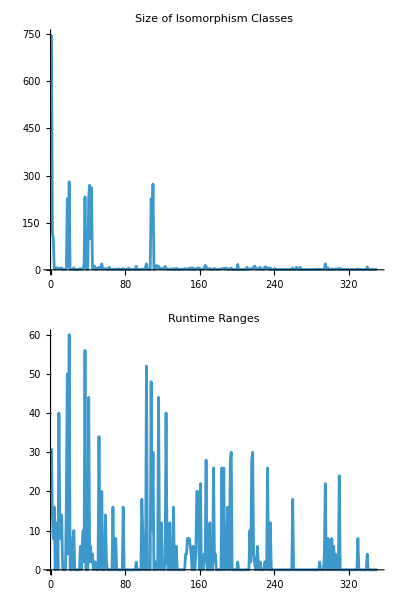

```mathematica
Column[With[{w=1600},{
ListPlot[
Length/@eqlgroups,
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Isomorphism Classes"
],
ListPlot[
haltdifs[[All,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Runtime Ranges"
]
}]]
```

Generally, spikes in the size of isomorphism classes, aside from the first, generally corresponds to spikes in runtime range, yet there are also some spikes where there is low runtime range.
Spikes in runtime ranges are more frequent. Some spikes correspond with large isomorphic classes, but there is a spike at group 295 where the size is very small. Large runtime ranges also happen during the large size spike in the beginning.

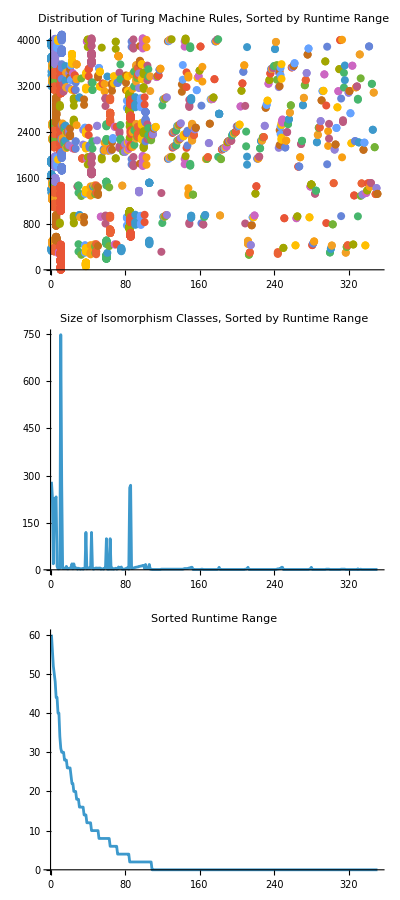

```mathematica
Column[With[{w=1600},{
ListPlot[
stackPoints[list[[All,2]]],
PlotRange->Full,
ImageSize->{w,Automatic},
AspectRatio->1/3,
PlotLabel->"Distribution of Turing Machine Rules, Sorted by Runtime Range"
],
ListPlot[
Length/@list[[All,2]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Isomorphism Classes, Sorted by Runtime Range"
],
ListPlot[
list[[All,1,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/8,
PlotLabel->"Sorted Runtime Range"
]
}]]
```

larger groups of equivalent rules generally correspond to a larger difference so we only pick the large groups??